```mathematica
WolframLanguadeData[]
```

```mathematica
WolframLanguageData[];
```

```mathematica
?WolframLanguageData
```

```mathematica
WolframLanguageData["Plot","DocumentationExampleInputs"][[1]]
```

```mathematica
WolframLanguageData["Write","PlaintextUsage"]//
```

```mathematica
(* For which errors I'm I trying to provide info *)
```

```mathematica
correct="Plot[5x^2,{x,0,2}]";
```

```mathematica
wrong=correct="Plot[5x^2,{x,0,2]}";
```

```mathematica
SyntaxInformation[Plot]
```

```mathematica
SyntaxInformation[Write]
```

```mathematica
Write["stdout"]
```

```mathematica
?Write
```

```mathematica
SyntaxInformation[GaussianFilter]
```

```mathematica
(* Maybe, compare the heads, *)
```

```mathematica
TreeForm[%2]
```

```mathematica
%2[[1,2]]
```

```mathematica
thislist= {1,1,2,1,4,3,4,3,2,4,2};
```

```mathematica
GaussianFilter[thislist,2]
```

```mathematica
SyntaxInformation[GaussianFilter][[1,2]]
```

```mathematica
Hold[GaussianFilter[thislist,2]]
```

```mathematica
%11
```

```mathematica
thislist=.
```

```mathematica
%11//TreeForm
```

```mathematica
Apply[Head,%91,1]// ReleaseHold
```

```mathematica
Thread[f[%91],3]
```

```mathematica
CMD + SHIFT + E
```

```mathematica
Apply@%11
```

Cell[BoxData[
 RowBox[{"Apply", "[", 
  RowBox[{"Hold", "[", 
   RowBox[{"GaussianFilter", "[", 
    RowBox[{"thislist", ",", "2"}], "]"}], "]"}]}]], "Output",
 CellChangeTimes->{{3.770720966573884*^9, 3.770720979950595*^9}},
 CellLabel->"Out[88]="]

```mathematica
%107//TreeForm
```

direct call to the parser:

```mathematica
FrontEndExecute[FrontEnd`ReparseBoxStructurePacket["Exp[1+2"]]
```

```mathematica
FrontEndExecute[FrontEnd`ReparseBoxStructurePacket["Exp[1+2]"]]
```

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
g[f[x]
```

```mathematica
FrontEndExecute[FrontEnd`ReparseBoxStructurePacket["g[f[x]"]]
```

```mathematica
Flatten@ReplaceRepeated[RowBox[{"g","[",RowBox[{"f","[","x","]"}]}], RowBox[{anything___}]:>{anything}]
```

```mathematica
Flatten@ReplaceRepeated[RowBox[{"g","[",RowBox[{"f","[","x","]"}]}], RowBox[{anything___}]:>{anything}]
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
flattenParse@parseString["Exp[1+2*(Sin[x]]"]
```

```mathematica
Names[""]
```

If names return a non empty list, I can use that as the head of the symbol //Cases

then get the syntax

Maybe list all the possible combinations of brackets...

```mathematica
Names["Exp"]
```

```mathematica
SyntaxInformation[Exp]
```

```mathematica
Names["Cos"]
```

```mathematica
...Exp[1+2+f[x,y],5]...
```

Try to construct all the possible trees: add bracket, remove bracket, moving bracket

```mathematica
SetAttributes[f,{HoldFirst}]
```

```mathematica
f[2+2,2+3]
```

```mathematica
ToString[2+2,InputForm]
```

```mathematica
"4"
```

```mathematica
ToString[..., InputForm]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
makeExpressionString[Exp[1+2 * 3]]
```

```mathematica
makeExpressionString[Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]]
```

```mathematica
StringPosition["Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]","]"]
```

```mathematica
StringDrop["Plot[{Sin[x] + x/2, Sin[x] + x}, {x, 0, 10}, Filling -> {1 -> {2}}]", {26,26}]
```

```mathematica
DeleteCases[flattenParse@parseString["Plot[{Sin[x] + x/2, Sin[x + x}, {x, 0, 10}, Filling -> {1 -> {2}}]"], " "]
```

```mathematica
{"Plot","[","{","Sin","[","x","]","+","x","/","2",",","Sin","[","x","+","x","}",",","{","x",",","0",",","10","}",",","Filling","->","{","1","->","{","2","}","}","]"}
```

```mathematica
"2 + 2"
```

```mathematica
stringExp=StringTake["HoldComplete[Exp[1 + 2 + Sin[x]]]" , {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
flattenParse@parseString[stringExp]
```

## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
?x
```

Missing[UnknownSymbol,x]

```mathematica
(* Do not run the next one *)
```

```mathematica
makeExpressionString[Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]]
```

```mathematica
Remove[x]
```

```mathematica
?x
```

### I will start with trigonometric functions that can only accept one argument

Choose an expression, then remove the final bracket for now:

```mathematica
myexpressionstring = "Exp[1+2 Sin[x]]"
```

Exp[1+2 Sin[x]]

```mathematica
myexpressionstring = "Exp[Sin[x]]"
```

```mathematica
bracketpositions=StringPosition[myexpressionstring,"]"]
```

{{14,14},{15,15}}

```mathematica
brackettodrop=bracketpositions[[-1]]
```

```mathematica
mybrokenexpressionstring= StringDrop[myexpressionstring,brackettodrop]
```

```mathematica
flattenParse@parseString[mybrokenexpressionstring]
```

```mathematica
myexpression=DeleteCases[flattenParse@parseString[mybrokenexpressionstring],"  "]
```

```mathematica
myexpression=DeleteCases[flattenParse@parseString[myexpressionstring]," "]
```

{Exp,[,1,+,2,Sin,[,x,],]}

```mathematica
StringJoin[myexpression]
```

Exp[1+2Sin[x]]

```mathematica
parseString[myexpressionstring]
```

```mathematica
myexpression
```

Tim said, that every time a [ is found, go a level down. Try to do that.

Or maybe start with turning the function names from String to objects

```mathematica
positions=Position[myexpression,_?NameQ]//Flatten
```

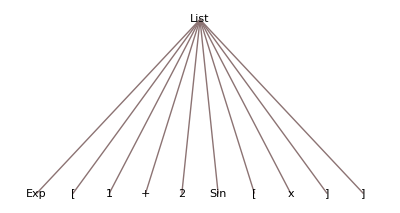

```mathematica
myexpression//TreeForm
```

```mathematica
StringCount[{"1","+","2","Sin","[","x","["},"["]//Total
```

2

```mathematica
StringCases[{"1","+","2","Sin","[","x"},"["]
```

{{},{},{},{},{[},{}}

## Playing with the expression:

```mathematica
myexpression
```

{Exp,[,1,+,2,Sin,[,x,],]}

### Continue with this one:

```mathematica
myexpression/. head_[before___,function_,"["_,body___, "]"_,after___]/;   If[Length[{body}]>0, Echo[{{body},{Total@StringCount[{body},"["],Total@StringCount[{body},"]"]}},"Before:"]]&& Total@StringCount[{body},"["]== Total@StringCount[{body},"]"]  && If[Length[{body}]>0, Echo[{"head:",head,"before:",before,"function:",function,"openbracket:",openbracket,"body:",body,"closebracket:",closebracket,"after:",after},"After:"]]->head[before,function[openbracket,body,closebracket],after]//TreeForm
```

Before: {{1,+,2,Sin,[,x},{1,0}}

Before: {{1,+,2,Sin,[,x,]},{1,1}}

After: {head:,List,before:,function:,Exp,openbracket:,[,body:,1,+,2,Sin,[,x,],closebracket:,],after:}

Before: {{x},{0,0}}

After: {head:,List,before:,Exp,[,1,+,2,function:,Sin,openbracket:,[,body:,x,closebracket:,],after:,]}

Before: {{x,]},{0,1}}

-Graphics-

```mathematica
myexpression//FullForm
```

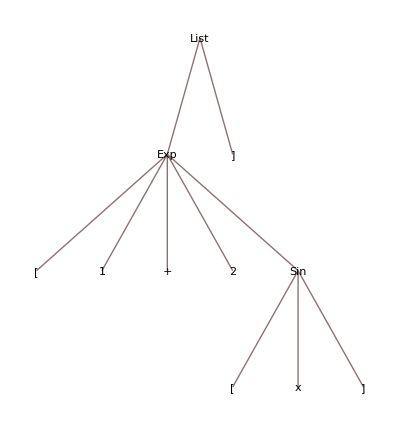

```mathematica
myexpression//. head_[before___,function_,openbracket_,body___,closebracket_,otherclosebracket___,after___]/;openbracket=="[" && closebracket=="]"&& otherclosebracket=="]" ->head[before,function[openbracket,body,closebracket,otherclosebracket],after]//TreeForm
```

```mathematica
myexpression//. {before___,function_String,openbracket_String,body___,closebracket_String,after___}/;openbracket=="[" && closebracket=="]" ->{before, function[openbracket,{body,closebracket}],after}//TreeForm;
```

```mathematica
myexpression//. {before___,function_String,openbracket_String,body___,closebracket_String,after___}/;openbracket=="[" && closebracket=="]" ->{before, function ,{openbracket,body,closebracket},after}//TreeForm;
```

```mathematica
mynewexpression=myexpression/. {function_,openbracket_String,body___,closebracket_String}/;openbracket=="[" && closebracket=="]" ->{ function,{openbracket,body,closebracket}}//TreeForm
```

```mathematica
mynewexpression//. List_Symbol[stuff___] ->stuff //TreeForm
```

```mathematica
Delete[x]
```

## Playing with the reverse expression

```mathematica
myexpressionreversed =Reverse[ myexpression,1]/. item_ /; item== "]" -> "Q"  /. item_/; item=="[" -> "]"/. item_ /; item=="Q" -> "[";
```

```mathematica
myexpressionreversed=myexpression//Reverse;
```

```mathematica
myexpressionreversed //TreeForm
```

```mathematica
myexpressionreversed[[4]]
```

```mathematica
StringCases[myexpressionreversed[[2;;4]],"]"]//Flatten
```

```mathematica
StringContainsQ["StyleBox[\"string\", \"TI\"]",patt]
```

```mathematica
Length@myexpressionreversed[[2;;4]]
```

```mathematica
AnyTrue
```

```mathematica
!AnyTrue[StringContainsQ["]"]]@myexpressionreversed[[2;;4]]
```

```mathematica
myexpression//Reverse//TreeForm
```

```mathematica
ReplaceRepeated[%194, List[{anything___}]:>{anything}]//TreeForm
```

```mathematica
myexpressionreversed//. head_[before___,closebracket_,body___,openbracket_,function_,after___] /;openbracket=="[" && closebracket=="]" &&  NoneTrue[StringContainsQ["]"]]@{body}->head[before,function,{closebracket,body,openbracket},after];
```

```mathematica
%165[[4]]//Head
```

```mathematica
mynewexpressionreversed=myexpressionreversed/. {openbracket_,body___,closebracket_,function_,therest___} /;openbracket=="[" && closebracket=="]" ->{{openbracket,body,closebracket,function},therest};mynewexpressionreversed//TreeForm
```

```mathematica
//. List_Symbol[stuff___] ->stuff;
```

```mathematica
mynewexpressionreversedcleaned = mynewexpressionreversed//.  {openbracket_,body___,closebracket_} /;openbracket=="[" && closebracket=="]" ->body;mynewexpressionreversedcleaned//TreeForm
```

```mathematica
Reverse[mynewexpressionreversed]/.  {_,closebracket_} /;closebracket=="]"  ->555//TreeForm
```

```mathematica
mynewexpressionreversed[[0]]//Head
```

```mathematica
Delete[x]
```

```mathematica
myexpression//TreeForm
```

```mathematica
Reverse[myexpression]//TreeForm
```

## Play with functions:

```mathematica
myexpression//TreeForm
```

-Graphics-

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"];
```

```mathematica
SyntaxInformation[Exp][[1,2]]//Length
```

1

```mathematica
[ [ [   ] ] ]
```